## 1D Symmetric

### Test

```mathematica
symClass=ChemDVRClass["Cartesian1DCsDVR"];
ChemDVRClear[symDVR];
symDVR=symClass[{100},{{-5, 5}}]
```

```mathematica
ChemDVRObject[…][]
```

```mathematica
Needs["ChemTools`DVR`"]
```

```mathematica
ChemDVRReload["SymmetricCartesian1DDVR"];
symClass=ChemDVRClass["SymmetricCartesian1DDVR"];
ChemDVRClear[symDVR];
symDVR=symClass[{100},{{-5, 5}}]
```

ChemDVRObject[…]

```mathematica
ke=symDVR[Return->"KineticEnergy"];
pe=symDVR[Return->"PotentialEnergy"];
```

```mathematica
wfns=symDVR[Return->"Wavefunctions"];
```

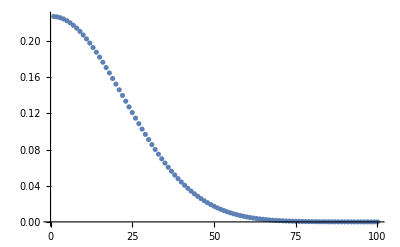
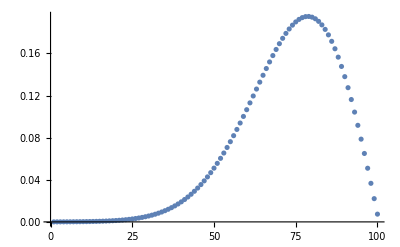
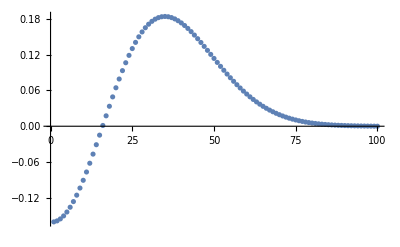

```mathematica
wfns[[2]]//Take[#, 3]&//Map[ListPlot]
```

```mathematica
symDVR[]
```

```mathematica
wfns[[1]]/wfns[[1,1]]
```

```mathematica
cartDVR[Return->"Wavefunctions"][[1]]
```

{0.357125,1.07138,1.78565,2.50011,3.21575,3.93641,4.67249,5.44312,6.27228,7.18079,8.18148,9.28011,10.4785,11.7768,13.1748,14.672,16.2679,17.9624,19.7551,21.6459,23.6346,25.7211,27.9052,30.187,32.5664,35.0432,37.6175,40.2893,43.0584,45.9249,48.8888,51.9501,55.1086,58.3646,61.7178,65.1683,68.7162,72.3613,76.1037,79.9435,83.8805,87.9148,92.0464,96.2753,100.601,105.025,109.546,114.164,118.879,123.691,128.601,133.608,138.713,143.914,149.213,154.61,160.103,165.694,171.382,177.168,183.05,189.031,195.108,201.283,207.554,213.924,220.39,226.954,233.615,240.374,247.229,254.183,261.233,268.381,275.626,282.968,290.408,297.945,305.579,313.311,321.14,329.067,337.089,345.211,353.428,361.745,370.156,378.668,387.273,395.979,404.778,413.68,422.671,431.769,440.951,450.246,459.616,469.114,478.734,487.494}

```mathematica
pe=symDVR[Return->"PotentialEnergy"];
```

```mathematica
symDVR[Function->Function[0]]
```

```mathematica
cartClass=ChemDVRClass["Cartesian1DDVR"];
cartDVR=cartClass[{100},{{-5,5}}]
```

ChemDVRObject[…]

```mathematica
wfns2=cartDVR[Return->"Wavefunctions"];
```

```mathematica
wfns2[[1]]/wfns2[[1,1]]
```

{1.,3.,5.00007,7.00067,9.00455,11.0225,13.0836,15.2415,17.5633,20.1072,22.9093,25.9856,29.3413,32.9768,36.8913,41.0836,45.5525,50.2973,55.3172,60.6117,66.1802,72.0227,78.1386,84.528,91.1904,98.126,105.334,112.816,120.57,128.596,136.896,145.468,154.312,163.429,172.819,182.481,192.415,202.622,213.101,223.853,234.877,246.174,257.743,269.584,281.698,294.085,306.743,319.674,332.878,346.354,360.102,374.122,388.415,402.981,417.819,432.929,448.312,463.967,479.895,496.095,512.567,529.312,546.329,563.62,581.182,599.017,617.124,635.504,654.155,673.081,692.277,711.748,731.489,751.505,771.791,792.352,813.183,834.289,855.665,877.316,899.236,921.433,943.898,966.64,989.649,1012.94,1036.49,1060.32,1084.42,1108.8,1133.44,1158.36,1183.54,1209.01,1234.73,1260.75,1286.99,1313.58,1340.52,1365.05}

```mathematica
wfns[[1]]/wfns[[1,1]]
```

{1.,1.,2.35532,2.35536,3.71284,3.71506,5.0511,5.09248,6.28546,6.56469,7.5819,8.26622,9.30778,10.2787,11.4443,12.6193,13.9333,15.2861,16.7549,18.2762,19.9017,21.5872,23.3701,25.2178,27.1584,29.167,31.2656,33.4344,35.6909,38.0194,40.434,42.9219,45.4946,48.1416,50.8725,53.6785,56.5674,59.5323,62.5794,65.7031,68.9084,72.1908,75.5542,78.9953,82.517,86.1166,89.7965,93.5548,97.3929,101.31,105.306,109.382,113.536,117.77,122.083,126.475,130.946,135.498,140.127,144.837,149.624,154.492,159.438,164.465,169.569,174.755,180.016,185.361,190.781,196.284,201.862,207.524,213.26,219.081,224.975,230.955,237.006,243.146,249.355,255.654,262.02,268.479,275.001,281.621,288.299,295.08,301.913,308.856,315.843,322.951,330.087,337.362,344.643,352.098,359.503,367.156,374.646,382.618,389.68,399.547}

### Cartesian1D Sanity Check

```mathematica
cartKE=cartDVR[Return->"KineticEnergy"];
cartPE=cartDVR[Return->"PotentialEnergy"];
```

```mathematica
transf2=
1/Sqrt[2]*With[{n=Length[cartKE]/2},
ArrayFlatten[{
{IdentityMatrix[n],Reverse/@IdentityMatrix[n]},
Reverse/@{IdentityMatrix[n],Reverse/@-IdentityMatrix[n]}
}]
];
```

```mathematica
realSoln=
ChemTools`Private`Hidden`ChemDVRDefaultWavefunctions[
transf2.cartKE.transf2,
cartPE
];
```

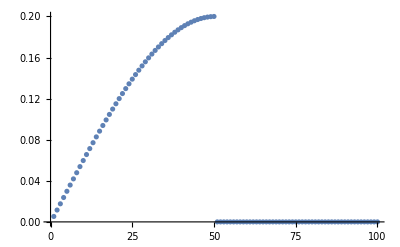
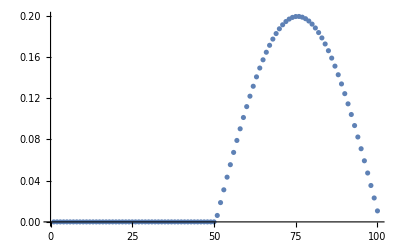
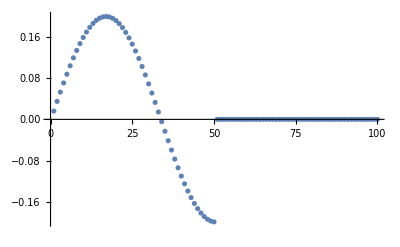

```mathematica
realSoln[[2]]//Take[#,3]&//Map[ListPlot]
```

### Transform

```mathematica
transf=
With[{n=2},
ArrayFlatten[{
{IdentityMatrix[n],Reverse/@IdentityMatrix[n]},
Reverse/@{IdentityMatrix[n],Reverse/@-IdentityMatrix[n]}
}]
];
```

```mathematica
torig=
Table[t[i,j],
{i,{2,1,-1,-2}},
{j,{2,1,-1,-2}}
]/.{
(t[i_,j_])/;(i<j):>t[-i,-j],
(t[i_?Positive,i_]):>t[-i,-i]
};
torig//MatrixForm
```

(t[-2,-2] | t[2,1] | t[2,-1] | t[2,-2]
t[-1,-2] | t[-1,-1] | t[1,-1] | t[1,-2]
t[1,-2] | t[1,-1] | t[-1,-1] | t[-1,-2]
t[2,-2] | t[2,-1] | t[2,1] | t[-2,-2])

```mathematica
tnew=
transf.torig.Inverse[transf]//FullSimplify;
tnew//MatrixForm
```

(t[-2,-2]+t[2,-2] | t[2,-1]+t[2,1] | 0 | 0
t[-1,-2]+t[1,-2] | t[-1,-1]+t[1,-1] | 0 | 0
0 | 0 | t[-1,-1]-t[1,-1] | t[-1,-2]-t[1,-2]
0 | 0 | -t[2,-1]+t[2,1] | t[-2,-2]-t[2,-2])

```mathematica
vecsorg=torig//Eigenvectors;
```

```mathematica
vecsnew=tnew//Eigenvectors;
```

```mathematica
vecsorg[[1,2]]
```

```mathematica
vecsnew[[1,1]]
```